```mathematica
Export["saddle.png",GraphicsRow[{Show[
Plot3D[Re[x+I y-1-Log[x+I y]],{x,0,2},{y,-1,1},BoxRatios->{1,1,3/4},AxesLabel->{"Re z","Im z","Re f(z)"},ViewPoint->{-1.3,-2.4,2}],
ParametricPlot3D[{y Cot[y],y,-1+y Cot[y]-1/2 Log[y^2+y^2 Cot[y]^2]},{y,-2,2},PlotStyle->Blue]/.Line[pts_]:>Tube[pts,.02],
ParametricPlot3D[{x,0,-1+x-Log[x^2]/2},{x,2/10,2},PlotStyle->Red]/.Line[pts_]:>Tube[pts,.02],
ParametricPlot3D[{1,y,0},{y,-1,1},PlotStyle->White]/.Line[pts_]:>Tube[pts,.02],PlotRangePadding->0,Background->RGBColor[0.15,0.15,0.15]
],
Show[
Plot3D[Re[x+I y-1-Log[x+I y]],{x,0,2},{y,-1,1},BoxRatios->{1,1,3/4},AxesLabel->{"Re z","Im z","Re f(z)"},ViewPoint->Top],
ParametricPlot3D[{y Cot[y],y,-1+y Cot[y]-1/2 Log[y^2+y^2 Cot[y]^2]},{y,-2,2},PlotStyle->Blue]/.Line[pts_]:>Tube[pts,.02],
ParametricPlot3D[{x,0,-1+x-Log[x^2]/2},{x,2/10,2},PlotStyle->Red]/.Line[pts_]:>Tube[pts,.02],
ParametricPlot3D[{1,y,0},{y,-1,1},PlotStyle->White]/.Line[pts_]:>Tube[pts,.02],PlotRangePadding->0,Background->RGBColor[0.15,0.15,0.15]
]},PlotRangePadding->0,ImageSize->740,Background->RGBColor[0.15,0.15,0.15]]]
```

saddle.png

```mathematica
Show[
Plot3D[Re[x+I y-1-Log[x+I y]],{x,0,2},{y,-1,1},BoxRatios->{1,1,3/4},AxesLabel->{"Re z","Im z","Re f(z)"}],
ParametricPlot3D[{y Cot[y],y,-1+y Cot[y]-1/2 Log[y^2+y^2 Cot[y]^2]},{y,-2,2},PlotStyle->Blue]/.Line[pts_]:>Tube[pts,.02],
ParametricPlot3D[{x,0,-1+x-Log[x^2]/2},{x,2/10,2},PlotStyle->Red]/.Line[pts_]:>Tube[pts,.02],
ParametricPlot3D[{1,y,0},{y,-1,1},PlotStyle->White]/.Line[pts_]:>Tube[pts,.02],PlotRangePadding->0,Background->RGBColor[0.15,0.15,0.15]
]
```

-Graphics3D-

```mathematica
nn=30;
Show[
ParametricPlot[{Cos[t],Sin[t]},{t,0,2 Pi}],
ListPlot[{Re[z],Im[z]}/.NSolve[Sum[(nn z)^k/k!,{k,0,nn-1}]==0,z],PlotStyle->{White,PointSize[0.015]}],
Axes->False,Frame->True,FrameLabel->{"Re z","Im z"},LabelStyle->Black,ImageSize->450,
Prolog->{RGBColor[0.15,0.15,0.15],Rectangle[Scaled[{0,0}],Scaled[{1,1}]]}
]
```

-Graphics-

```mathematica
p1=0.5;
f[x_]:=1/(Cot[1/2]-1/2 Csc[1/2]^2) (x-1/2 Cot[1/2])+1/2;
Show[
ParametricPlot[{Cos[t],Sin[t]},{t,0,2 Pi},PlotStyle->{Opacity[0],RGBColor[0.560181,0.691569,0.194885],Thick}],
ContourPlot[x^2+y^2==E^(2 x-2),{x,-1/2,2},{y,-3/2,3/2},PlotPoints->70,ContourStyle->{RGBColor[0.922526,0.385626,0.209179],Thickness[0.005],Opacity[0.4]}],
RegionPlot[x^2+y^2<E^(2 x-2),{x,-1/2,2.3},{y,-3/2,3/2},PlotPoints->70,PlotStyle->{RGBColor[0.922526,0.385626,0.209179],Opacity[0.2]},BoundaryStyle->None],
ParametricPlot[{1,0}+{Cos[t],Sin[t]} r,{t,0,2 Pi},{r,0,1/2},PlotStyle->{RGBColor[1,0.75,0],Opacity[0.175]},BoundaryStyle->None],
ParametricPlot[{y Cot[y],y},{y,-3/2,3/2},PlotStyle->{Thickness[0.01],Dashing[{0.04,0.02}]}],
ParametricPlot[{y Cot[y],y},{y,-1/2,1/2},PlotStyle->{Thickness[0.005],White}],
ParametricPlot[BezierFunction[{{1/2 Cot[1/2],1/2},{p1,f[p1]},{-2,1.8},{-1.5,0},{-2,-1.8},{p1,-f[p1]},{1/2 Cot[1/2],-1/2}}][t],{t,0,1},PlotStyle->{Thickness[0.005],White}],
PlotRange->All,Axes->False,Frame->True,ImageSize->650,PlotRangePadding->{{0.41,0},{0,0}},LabelStyle->Black,FrameLabel->{"Re s","Im s"},
Epilog->{Text[Style["γ",White,24,FontFamily->"Times"],{-1.275,0.7}],Text[Style["U_γ",RGBColor[1,0.75,0],24,FontFamily->"Times"],{1.2,-0.6}],Text[Style["Re φ(s)>0",RGBColor[0.922526,0.385626,0.209179],24,FontFamily->"Times"],{1.85,0.38}],Text[Style["steepest descent\npath",RGBColor[0.368417,0.506779,0.709798],24,FontFamily->"Times"],{1.1,1.1}]},
Prolog->{RGBColor[0.15,0.15,0.15],Rectangle[Scaled[{0,0}],Scaled[{1,1}]]}
]
```

-Graphics-

```mathematica
ColorData[97,"ColorList"]
ColorData[97,"ColorList"][[3]]
ColorData[97,"ColorList"][[3]]//InputForm
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

RGBColor[0.560181, 0.691569, 0.194885]

RGBColor[0.560181, 0.691569, 0.194885]

```mathematica
nn=30;
Show[
ParametricPlot[{Cos[t],Sin[t]},{t,0,2 Pi}],
ContourPlot[x^2+y^2==E^(2 x-2),{x,-1/2,1},{y,-1/2,1/2},PlotPoints->70,ContourStyle->{RGBColor[0.922526,0.385626,0.209179],Thickness[0.01]}],
ListPlot[{Re[z],Im[z]}/.NSolve[Sum[(nn z)^k/k!,{k,0,nn-1}]==0,z],PlotStyle->{White,PointSize[0.0125]}],
Axes->False,Frame->True,FrameLabel->{"Re z","Im z"},LabelStyle->Black,ImageSize->450,
Prolog->{RGBColor[0.15,0.15,0.15],Rectangle[Scaled[{0,0}],Scaled[{1,1}]]},
Epilog->{Text[Style["S",RGBColor[0.922526,0.385626,0.209179],24,FontFamily->"Times"],{0.3,0}]}
]
```

-Graphics-

```mathematica
p[n_,z_]:=Sum[z^k/k!,{k,0,n}];
```

0.+0.367879 ⅈ

-1.20292

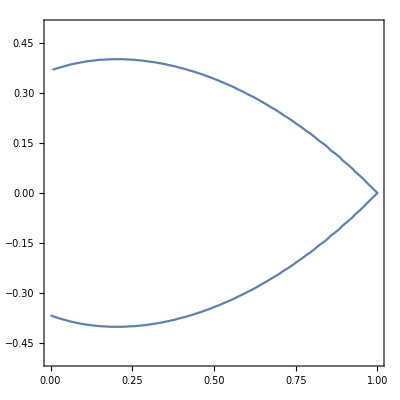

```mathematica
θ=Pi/2;
ξ=r E^(I θ)/.FindRoot[r E^(1-r Cos[θ])==1,{r,0.7}]
τ=Im[ξ-1-Log[ξ]]
τn[n_]:=Mod[τ n,2 Pi,-Pi];
Show[
ContourPlot[(x^2+y^2) E^(2-2 x)==1,{x,0,1},{y,-1/2,1/2},AspectRatio->1],
Graphics[{White,Point[{Re[ξ],Im[ξ]}]}]
]
```

```mathematica
zz[n_,w_]:=ξ (1+Log[n]/(2 (1-ξ) n)-(w-I τn[n])/(1-ξ)/n);
```

```mathematica
m=100;
rangex=15;rangey=15;
```

```mathematica
Show[ParametricPlot[{Sin[t],Cos[t]}/10,{t,0,2 Pi},PlotStyle->Opacity[0]],
ContourPlot[x^2+y^2==E^(2 x-2),{x,-1/2,1},{y,-1/2,1/2},PlotPoints->70,ContourStyle->{RGBColor[0.922526,0.385626,0.209179],Thickness[0.005]}],
ListPlot[{Re[z],Im[z]}/.NSolve[p[m-1,m z]==0,z,WorkingPrecision->20],PlotStyle->{White,PointSize[0.01]}],
Graphics[{PointSize[0.014],RGBColor[1,0.75,0],Point[{Re[ξ],Im[ξ]}]}],Graphics[{EdgeForm[{AbsoluteThickness[4],RGBColor[0.368417,0.506779,0.709798]}],FaceForm[],Polygon[{{Re[zz[m,-rangex-rangey I]],Im[zz[m,-rangex-rangey I]]},{Re[zz[m,rangex-rangey I]],Im[zz[m,rangex-rangey I]]},{Re[zz[m,rangex+rangey I]],Im[zz[m,rangex+rangey I]]},{Re[zz[m,-rangex+rangey I]],Im[zz[m,-rangex+rangey I]]}}]}],
PlotRange->{{-0.325,1},{-0.475,0.8}},Axes->False,Frame->True,ImageSize->720,LabelStyle->Black,
Prolog->{RGBColor[0.15,0.15,0.15],Rectangle[Scaled[{0,0}],Scaled[{1,1}]]},
Epilog->{Text[Style["ξ",RGBColor[1,0.75,0],24,FontFamily->"Times"],{0.08,0.33}]}
]
```

-Graphics-

```mathematica
m=.;
images=Table[
Show[ParametricPlot[{Sin[t],Cos[t]}/10,{t,0,2 Pi},PlotStyle->Opacity[0]],
ContourPlot[x^2+y^2==E^(2 x-2),{x,-1/2,1},{y,-1/2,1/2},PlotPoints->70,ContourStyle->{RGBColor[0.922526,0.385626,0.209179],Thickness[0.005]}],
ListPlot[{Re[z],Im[z]}/.NSolve[p[m-1,m z]==0,z,WorkingPrecision->20],PlotStyle->{White,PointSize[0.01]}],
Graphics[{PointSize[0.014],RGBColor[1,0.75,0],Point[{Re[ξ],Im[ξ]}]}],Graphics[{EdgeForm[{AbsoluteThickness[4],RGBColor[0.368417,0.506779,0.709798]}],FaceForm[],Polygon[{{Re[zz[m,-rangex-rangey I]],Im[zz[m,-rangex-rangey I]]},{Re[zz[m,rangex-rangey I]],Im[zz[m,rangex-rangey I]]},{Re[zz[m,rangex+rangey I]],Im[zz[m,rangex+rangey I]]},{Re[zz[m,-rangex+rangey I]],Im[zz[m,-rangex+rangey I]]}}]}],
PlotRange->{{-0.325,1},{-0.475,0.8}},Axes->False,Frame->True,ImageSize->720,LabelStyle->Black,
Prolog->{RGBColor[0.15,0.15,0.15],Rectangle[Scaled[{0,0}],Scaled[{1,1}]]},
Epilog->{Text[Style["ξ",RGBColor[1,0.75,0],24,FontFamily->"Times"],{0.08,0.33}]}
],
{m,20,100,1}];
```

```mathematica
Export["scalinglimit.gif",images,"DisplayDurations"->1/10]
```

scalinglimit.gif

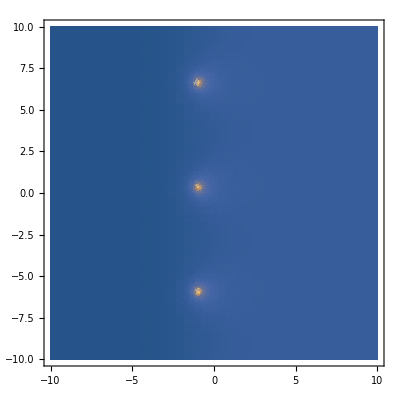

```mathematica
DensityPlot[1/Abs[E^(-x-I y)-(1-ξ) Sqrt[2 Pi]],{x,-10,10},{y,-10,10},PlotPoints->40,PlotRange->All]
```

```mathematica
FindRoot[E^(-w)==(1-ξ) Sqrt[2 Pi],{w,-1}]
```

{w→-0.982403+0.352513 ⅈ}

```mathematica
zz[50,w]/.FindRoot[E^(-w)==(1-ξ) Sqrt[2 Pi],{w,-1}]
```

-0.0221277+0.381359 ⅈ

```mathematica
Nearest[z/.NSolve[p[49,50 z]==0,z],-0.022127671093613882+0.3813587715988685 ⅈ]
```

{-0.0227486+0.380855 ⅈ}

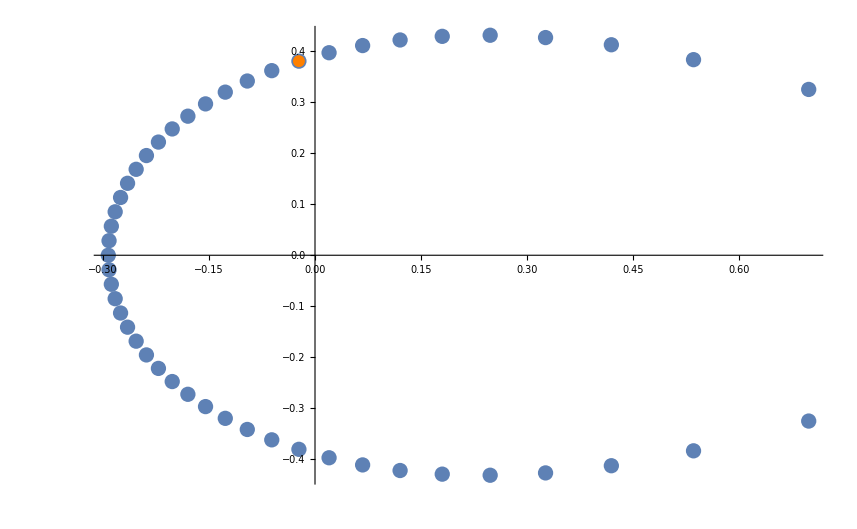

```mathematica
Show[
ListPlot[{Re[z],Im[z]}/.NSolve[p[49,50 z]==0,z]],
Graphics[{Orange,PointSize[0.01],Point[{-0.02274855819106452,0.3808553506231771}]}]
]
```